0

2.

2

3.6

2

1.6

0

0

2.56125

0

x^2+y^2

(-2.56125+x)^2+y^2

((-2.56125+x)^2+y^2)^a2 (x^2+y^2)^a1

((-2.56125+x)^2+y^2)^a2 (x^2+y^2)^a1

π/2-If[y>0,(ArcTan[y-y1,x-x1] a1+ArcTan[y-y2,x-x2] a2)/(a1+a2),(ArcTan[-y-y1,x-x1] a1+ArcTan[-y-y2,x-x2] a2)/(a1+a2)]

1

1.5

{{x→3.16463},{x→1.61731},{x→0.501898},{x→-0.30557}}

1.88496

108.

cut

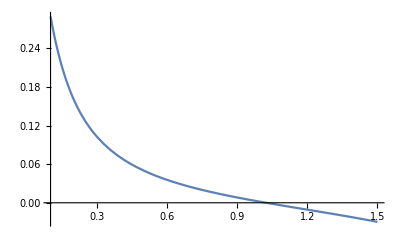

{x→1.0245}

2

-1.28062

5

60

{5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175}

{48.,53.,58.,63.,68.,73.,78.,83.,88.,93.,98.,103.,108.,113.,118.,123.,128.,133.,138.,143.,148.,153.,158.,163.,168.}

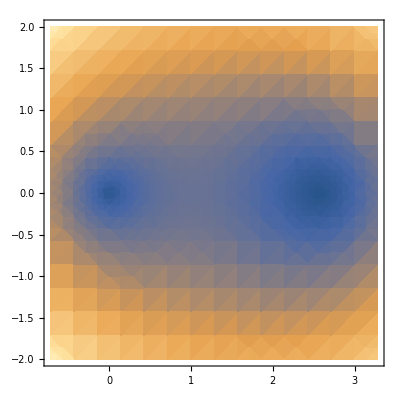

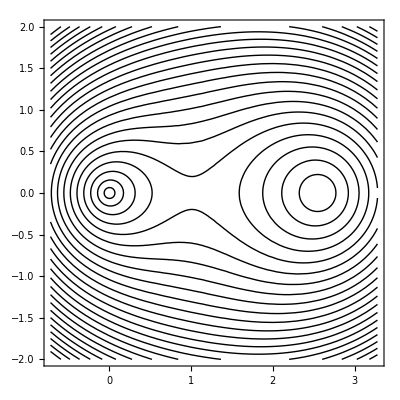

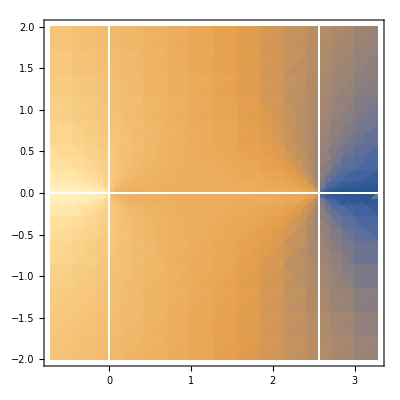

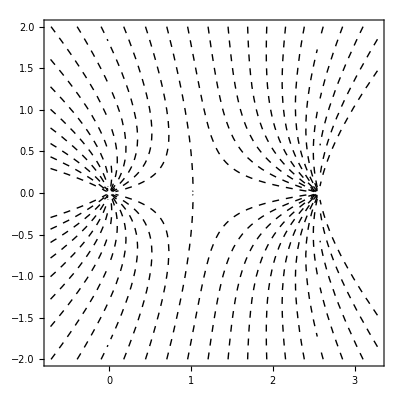

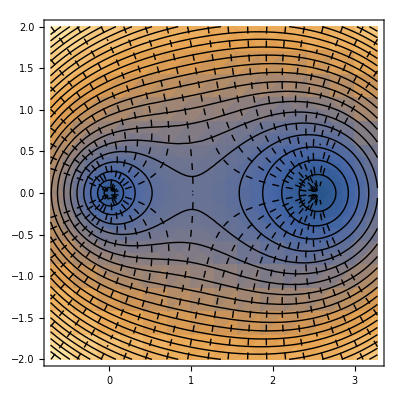

3083/5000

0.6166

```mathematica
Clear[x1,x2,y1,y2,x,y,f,g,a1,a2,s1]

xs1=0
ys1=2.0
xs2=2
ys2=3.6

xd = xs2-xs1
yd = ys2-ys1

x1 = 0
y1  =0
x2 = Sqrt[xd xd + yd yd]
y2 = 0

d1 = (x-x1)^2 + (y-y1)^2
d2 = (x-x2)^2 + (y-y2)^2

f = d1^a1 d2^a2
f2[x_,y_] = f

g[x_,y_] =Pi/2 -  If[y>0,
(ArcTan[(y-y1),(x-x1)] a1 + ArcTan[(y-y2),(x-x2)] a2)/(a1+a2),
(ArcTan[(-y-y1),(x-x1)] a1 + ArcTan[(-y-y2),(x-x2)] a2)/(a1+a2)
]

a1 =1
a2 = 1.5

NSolve[f2[x,0] == 2.2,x]

s0=Pi/2 - (π(a1-a2))/(2 (a1+a2))
sgrad= 180 s0/Pi

Print["cut"]
Plot[g[q,0.1] - s0,{q,0.1,1.5}]

FindRoot[g[x,0.001] == s0,{x,x2/2}]

gg =2
shift = -(x2+x1)/2

delta = 5
range=60
lst = Range[5,175,delta]
lst = Range[sgrad-range,sgrad+range,delta]
c0=DensityPlot[f^(1/(a1+a2)),{x,-gg-shift,gg-shift},{y,-gg,gg}]
c1=ContourPlot[f^(1/(a1+a2)),{x,-gg-shift,gg-shift},{y,-gg,gg},Contours->25,ContourShading->None]
c2=DensityPlot[180*g[x,y]/Pi,{x,-gg-shift,gg-shift},{y,-gg,gg}]
c3=ContourPlot[180*g[x,y]/Pi,{x,-gg-shift,gg-shift},{y,-gg,gg},Contours->lst,ContourShading->None, ContourStyle->Dashed]
Show[c0,c1,c3]
ug = -0.399141985852705;
og = 2.67494;

h = 10^(-2);
res=h*h*ParallelSum[If[f2[x,y]< 2.2, 1,0],{x,-ug,og,h},{y,0,1,h}]
N[res,32]
```